# GraphPlot

```mathematica
?GraphPlot
```

GraphPlot[g] generates a plot of the graph g.
GraphPlot[{v_i1→v_j1,v_i2→v_j2,…}] generates a plot of the graph in which vertex v_ik is connected to vertex v_jk.
GraphPlot[{{v_i1→v_j1,lbl_1},…}] associates labels lbl_k with edges in the graph.
GraphPlot[m] generates a plot of the graph represented by the adjacency matrix m.

```mathematica
words=DictionaryLookup["wol*"];
```

```mathematica
g=Flatten[Map[(Thread[#->DeleteCases[Nearest[words,#,3],#]])&,words]];
```

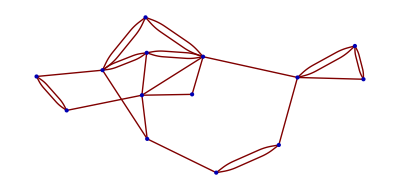
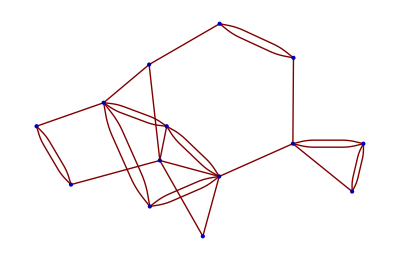
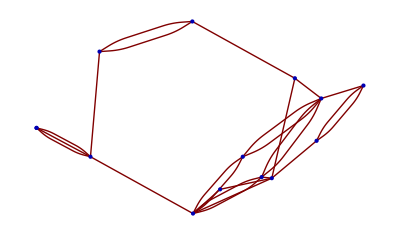
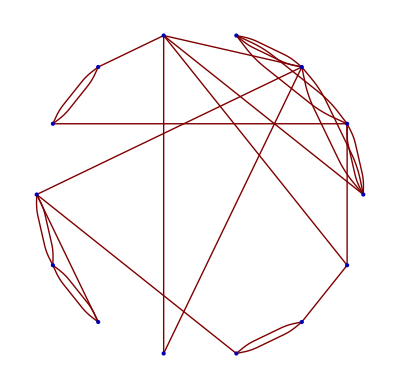
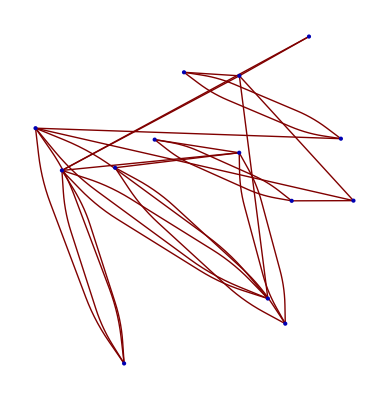
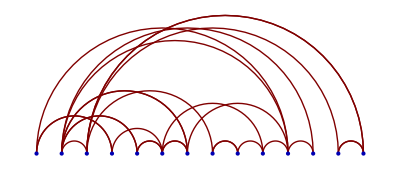

```mathematica
GraphPlot[g,Method->#]&/@{"SpringElectricalEmbedding","SpringEmbedding","HighDimensionalEmbedding","CircularEmbedding","RandomEmbedding","LinearEmbedding"}
```